## Compute the successor of a triangular matrix for the prombs algorithm

```mathematica
A[L_]:=Table[If[j≥i,f[Subscript[b, i,j]],0],{i,1,L},{j,1,L}]
succ[A_]:=Module[{As},
As=A;
As[[1;;-2,1;;-2]]=A[[2;;-1,2;;-1]];
As[[1;;-1,-1]]=0;
As[[-1,-1]]=1;
As]
```

## ProMBS

```mathematica
prombs[A_,fe_,g_,N_]:=Module[{Ar},
Ar=NestList[succ,A,N]/.f->fe;
g Reverse[Fold[Dot,Ar[[1]],Ar[[2;;-1]]][[1]]]]
prombsExt[A_,f_,g_,h_,ϵ_,N_]:=
1/ϵ(prombs[A,f[#] Exp[ϵ h[#]]&,g,N]-prombs[A,f,g,N])
```

## Model

```mathematica
(* Count statistics *)
ns[bij_]:=Module[{i,j},
{i,j}=bij/.Subscript[b, i_,j_]->{i,j};
Plus@@successes[[i;;j]]]
nf[bij_]:=Module[{i,j},
{i,j}=bij/.Subscript[b, i_,j_]->{i,j};
Plus@@failures[[i;;j]]]
```

```mathematica
fe[bij_]:=Beta[ns[bij]+σ,nf[bij]+γ]/Beta[σ,γ]
P["B"]:=Table[1/Binomial[L-1,m],{m,0,L-1}];
P["D"]:=Plus@@prombs[A[L],fe,P["B"],L-1];
```

## Example with binomial data

```mathematica
(* Data *)
L=6;
successes={2,3,2,4,7,7};
failures = {8,7,7,6,3,2};
(* Parameters *)
σ=1; (* in the paper: α = (σ, γ) *)
γ=1;
```

## ProMBS test

```mathematica
(* Compute the evidence P(D) *)
prombs[A[L],fe,P["B"],L]//Log//N
Plus@@prombs[A[L],fe,P["B"],L-1]//N
```

{-41.3506,-38.624,-38.6421,-38.9523,-39.3645,-39.8822}

5.93503×10^-17

```mathematica
prombsExt[A[L],fe,P["B"],-Log[fe[#]]&,0.0001,L]//Log//N
```

{-37.6264,-34.9842,-34.9932,-35.2918,-35.6921,-36.1942}

## Differential Entropy

```mathematica
(* Single bin entropy *)
H[bij_]:=Log[Beta[ns[bij]+σ,nf[bij]+γ]]+(ns[bij]+σ+nf[bij]+γ-2)PolyGamma[ns[bij]+σ+nf[bij]+γ]-(ns[bij]+σ-1)PolyGamma[ns[bij]+σ]-(nf[bij]+γ-1)PolyGamma[nf[bij]+γ]//N
```

```mathematica
Plus@@prombsExt[A[L],fe,P["B"],H,0.00000000001,L-1]/Plus@@prombs[A[L],fe,P["B"],L-1]//N
```

-2.92534

## Multibin Entropy

```mathematica
Hmb["D",ϵ_]:=1/P["D"]( prombsExt[A[L],fe,P["B"],-Log[fe[#]]&,ϵ,L-1]-prombs[A[L],fe,Log[P["B"]/P["D"]]P["B"],L-1])
Hmb["D",0.00000001]//N
```

{0.0739513,0.64034,0.918233,0.763885,0.475018,0.202872}

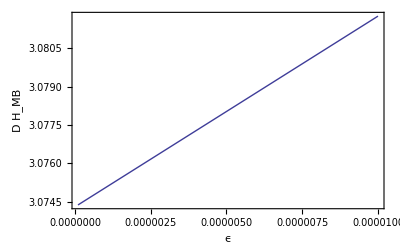

```mathematica
ListPlot[Table[{ϵ,Plus@@Hmb["D",ϵ]},{ϵ,0,0.00001,0.0000001}],
Frame->True,
Joined->True,
FrameLabel->{ϵ,Subscript[H, MB](D)},
PlotRange->All]
```

```mathematica
HmbLApprox["D",ϵ1_,ϵ2_]:=Module[{p1,p2},
p1=1/P["D"]( prombsExt[A[L],fe,P["B"],-Log[fe[#]]&,ϵ1,L-1]-prombs[A[L],fe,Log[P["B"]/P["D"]]P["B"],L-1]);
p2=1/P["D"]( prombsExt[A[L],fe,P["B"],-Log[fe[#]]&,ϵ2,L-1]-prombs[A[L],fe,Log[P["B"]/P["D"]]P["B"],L-1]);
p1-(p2-p1)/(ϵ2-ϵ1)ϵ1]
```

```mathematica
(* Vanilla method *)
```

```mathematica
Plus@@Hmb["D",0.00000001]
```

3.0743

```mathematica
(* Linear Approximation *)
```

```mathematica
Plus@@HmbLApprox["D",0.0002,0.0001]
```

3.0741

```mathematica
(* Exact Solution *)
```

```mathematica
Limit[Plus@@Hmb["D",ϵ],ϵ->0]//N
```

3.07429

## KL-Divergence

```mathematica
expectation[x_,y_]:=Module[{evidenceref,evidence},
evidenceref=P["D"];
If[y==1,successes[[x]]++,failures[[x]]++];
evidence=P["D"];
If[y==1,successes[[x]]--,failures[[x]]--];
evidence/evidenceref];
utility[x_,y_]:=Module[{result,fc,fn,fs,p},
p=expectation[x,y];
fc[bij_,z_]:=Module[{i,j},
{i,j}=bij/.Subscript[b, i_,j_]->{i,j};
If[i ≤x∧x≤j∧y==z,1,0]];
fn[bij_]:=Module[{},
If[y==1,ns[bij]+σ,nf[bij]+γ]];
fs[bij_]:=Module[{i,j},
{i,j}=bij/.Subscript[b, i_,j_]->{i,j};

Beta[ns[bij]+σ+fc[bij,1],nf[bij]+γ+fc[bij,2]]/Beta[σ,γ] If[i ≤x∧x≤j,Log[fn[bij]/(ns[bij]+σ+nf[bij]+γ)/p],1]];
result=N[1/P["D"] Plus@@prombs[A[L],fs,P["B"],L-1]];
result]
```

```mathematica
Table[utility[x,y],{y,1,2},{x,1,L}]
```

{{0.00154496,0.00211361,0.0031301,0.0127372,0.00493715,0.00228657},{0.000664496,0.000976715,0.00156297,0.00940154,0.00786468,0.00420839}}